## cos^4 init cond of dirichlet cons test

```mathematica
Clear[vec,CC,cos,u,dx,dy,dz,curlu,curlu2,x,y,z];
dx=0;
dy=0;
dz=0;
CC=10;
vec = {(y-dy),-(x-dx),0};
cos4= (Cos[CC*((x-dx)^2+(y-dy)^2+(z-dz)^2)])^4;
u[x_,y_,z_]=vec*cos4;
u[x,y,z]//MatrixForm//TraditionalForm
w=Curl[u[x,y,z],{cx,y,z}];
w//MatrixForm//TraditionalForm
```

(y cos^4(10 (x^2+y^2+z^2))
-x cos^4(10 (x^2+y^2+z^2))
0)

(-80 x z sin(10 (x^2+y^2+z^2)) cos^3(10 (x^2+y^2+z^2))
-80 y z sin(10 (x^2+y^2+z^2)) cos^3(10 (x^2+y^2+z^2))
80 y^2 sin(10 (x^2+y^2+z^2)) cos^3(10 (x^2+y^2+z^2))-cos^4(10 (x^2+y^2+z^2)))

## radius where u and w vanish:

```mathematica
R=1/2*Sqrt[2*Pi/CC];
x=0.13;
y=0;
z=Sqrt[R^2-y^2-x^2];
u[x,y,z]
u[x,0.2,z]
```

{0.,-1.82754×10^-66,0}

{0.00459934,-0.00298957,0}

## not used in thesis: cos^2 init cond (2D) of dirichlet cons test

```mathematica
Clear[vec,CC,cos,u,dx,dy,dz,curlu,curlu2,x,y,z];
CC=10;
cos=Cos[CC*(x^2+y^2)]*Cos[CC*(x^2+y^2)];
u[x_,y_]=cos*{y,-x};
u1=Dot[u[x,y],{1,0}];
u2=Dot[u[x,y],{0,1}];
curlu[x_,y_]=D[u2,x]-D[u1,y];
u[x,y]//MatrixForm//TraditionalForm
curlu[x,y]//TraditionalForm
```

(y cos^2(10 (x^2+y^2))
-x cos^2(10 (x^2+y^2)))

-2 cos^2(10 (x^2+y^2))+40 x^2 sin(10 (x^2+y^2)) cos(10 (x^2+y^2))+40 y^2 sin(10 (x^2+y^2)) cos(10 (x^2+y^2))

## radius where u and w vanish:

```mathematica
R=1/2*Sqrt[2*Pi/CC];
x=0.13;
y=Sqrt[R^2-x^2];
u[x,y]
curlu[x,y]
```

{1.4038×10^-33,-4.87422×10^-34}

3.84734×10^-16

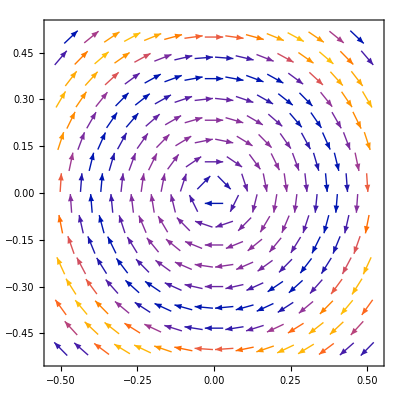

```mathematica
Clear[x,y];
p1=VectorPlot3D[u[x,y,z],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}];
p2=VectorPlot[u[x,y],{x,-0.5,0.5},{y,-0.5,0.5}];
Show[p2]
```